```mathematica
Get["http://iagomendes.com/GRVis.wl"]
```

Successfully loaded GRVis (version 1.0)

## Isotropic Schwarzschild

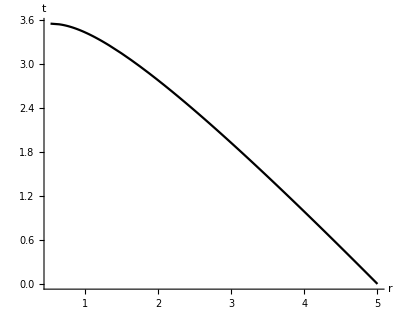

```mathematica
coords = {t, r, theta, phi}
M = 1;
metric = ({{-(1-M/(2 r))/(1 + M/(2 r)), 0, 0, 0}, {0, (1-M/(2 r))^4, 0, 0}, {0, 0, (1-M/(2 r))^4 r^2, 0}, {0, 0, 0, (1-M/(2 r))^4 r^2 Sin[theta]^2}})
geodesics[{
{{0,5,Pi/2,0}, lorentzFactor[0.9999999]*{1,-0.9999999,0,0}, 0.00131735}
}]
```

## Eddington-Finkelstein Schwarzschild

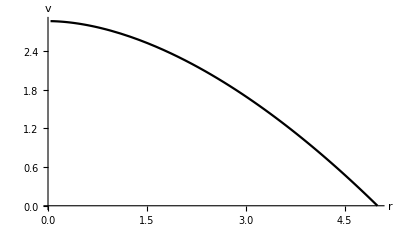

```mathematica
coords = {v, r, theta, phi}
M = 1;
metric = {
{-(1-2*M/r), 1, 0, 0},
{1, 0, 0, 0},
{0, 0, r^2, 0},
{0, 0, 0, r^2*Sin[theta]^2}
}
geodesics[{
{{0,5,Pi/2,0}, lorentzFactor[0.9999999]*{1,-0.9999999,0,0}, 0.001478}
}]
```